```mathematica
ClearAll["Global'*"]
a:=Plot[PrimePi[x],{x,0,1000},AxesLabel->{"Search Size",Automatic},PlotLabel->"Number of Primes Less Than Search Size"]
```

```mathematica
b:=Plot[PrimePi[x]/x,{x,0,1000},AxesLabel->{"Search Size",Automatic},PlotLabel->"Prime Density"]
```

```mathematica
c:=Labeled[Plot[{PrimePi[x]/x,1/Log[x]},{x,0,1000},Filling->{1->{2}},PlotLabel->"(π (x))/x ~ li(x)",LabelStyle->Directive[Blue, Bold]],{"Prime Density","x"},{Left,Bottom},RotateLabel->True]
```

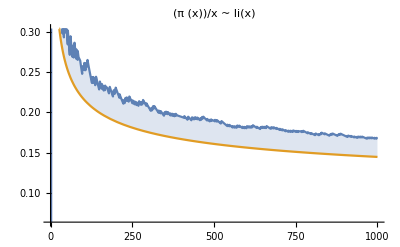
-Graphics-Prime Densityx

```mathematica
c
```

```mathematica
d:=Labeled[Plot[{PrimePi[x],x/Log[x]},{x,0,1000},Filling->{1->{2}},PlotLabel->"π(x) ~ x/(ln (x))",LabelStyle->Directive[Blue, Bold]],{"Number of primes < x","x"},{Left,Bottom},RotateLabel->True]
```

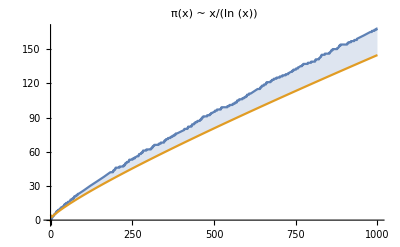
-Graphics-Number of primes < xx

```mathematica
d
```

```mathematica
CountPrime=Asymptotic[PrimePi[x],x->Infinity]
```

x/Log[x]

```mathematica
LogarithmicIntegral=Asymptotic[x/Log[x],x->Infinity]
```

x/Log[x]

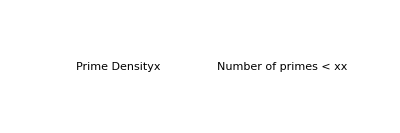

```mathematica
GraphicsRow[{c,d},AspectRatio->Automatic]
```